```mathematica
Graphics3D[{EdgeForm[{Thick}],FaceForm[{Red,Opacity[0.2]}],Icosahedron[]},Boxed->False,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

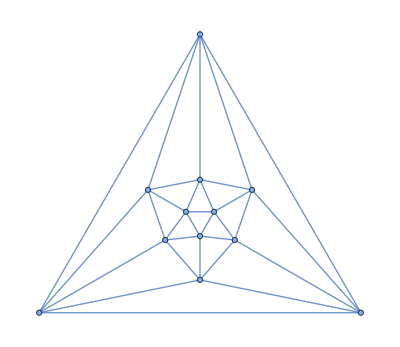

```mathematica
icoData=PolyhedronData["Icosahedron","SkeletonGraph"]
PlanarGraph[IconData]
verts=PolyhedronData["Icosahedron","VertexCoordinates"];
```

```mathematica
poly:=Cases[Normal@Geodesate[PolyhedronData["Icosahedron","Faces"],6],_Polygon,Infinity];
Graphics3D[{GeodesicPolyhedron["Icosahedron",6],poly[[1]]},Boxed->False]
```

-Graphics3D-